# Ricci - inverse gravity: integration

## Diff eq. with CC

```mathematica
(* equations *)

Clear[α];xisecd=1/(9 (6+5 xi[n]) α)(xi[n] (6+5 xi[n])^2 (9 (16+α)+6 xi[n] (40+α)+xi[n]^2 (100+α))+6 (6+5 xi[n])^4 ome[n]-27 (6+11 xi[n]+5 xi[n]^2) α xi'[n]+135 α (xi'[n])^2);
omed=-(3+2*xi[n])*ome[n];
omegaa:=-α((xi+3)^2*(5*xi+6)-18*xi')/(4*(5*xi+6)^3)
```

```mathematica
Clear[xi,α,w];

t0=.5;α=-4;

w=0;

Clear[dsol,xis,omes];dsol[ti_,xi0_,om0_]:=NDSolve[{xi''[n]==xisecd,ome'[n]==omed,xi'[ti]==0,xi[ti]==xi0,ome[ti]==om0},{xi,ome},{n,ti,t0}];
xis[ti_,xi0_,om0_,n_]:=(xi/.dsol[ti,xi0,om0][[1]])[n]
xisp[ti_,xi0_,om0_,nx_]:=D[xis[ti,xi0,om0,n],n]/.n->nx;
omes[ti_,xi0_,om0_,n_]:=(ome/.dsol[ti,xi0,om0][[1]])[n]
omegaas[ti_,xi0_,om0_,n_]:=-α((xis[ti,xi0,om0,n]+3)^2*(5*xis[ti,xi0,om0,n]+6)-18*xisp[ti,xi0,om0,n])/(4*(5*xis[ti,xi0,om0,n]+6)^3)
```

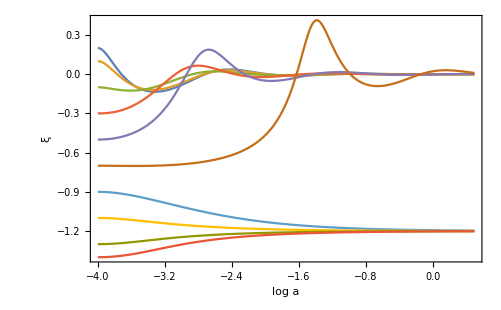

```mathematica
(* om_in=0.1 *)
om0x=0.1;Plot[{xis[-4,.2,om0x,t]/.t->tx,xis[-4,.1,om0x,t]/.t->tx,xis[-4,-.1,om0x,t]/.t->tx,xis[-4,-.3,om0x,t]/.t->tx,xis[-4,-.5,om0x,t]/.t->tx,xis[-4,-.7,om0x,t]/.t->tx,xis[-4,-.9,om0x,t]/.t->tx,xis[-4,-1.1,om0x,t]/.t->tx,,xis[-4,-1.3,om0x,t]/.t->tx,xis[-4,-1.4,om0x,t]/.t->tx},{tx,-4,t0},Frame->True,FrameLabel->{"log a","ξ"},BaseStyle->{Large,FontFamily->"Times",FontSize->18}]
```

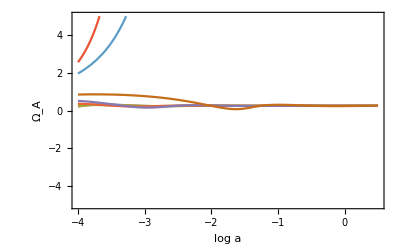

```mathematica
Plot[{omegaas[-4,.2,om0x,t]/.t->tx,omegaas[-4,.1,om0x,t]/.t->tx,omegaas[-4,-.1,om0x,t]/.t->tx,omegaas[-4,-.3,om0x,t]/.t->tx,omegaas[-4,-.5,om0x,t]/.t->tx,omegaas[-4,-.7,om0x,t]/.t->tx,omegaas[-4,-.9,om0x,t]/.t->tx,omegaas[-4,-1.1,om0x,t]/.t->tx,,omegaas[-4,-1.3,om0x,t]/.t->tx,omegaas[-4,-1.4,om0x,t]/.t->tx},{tx,-4,t0},Frame->True,PlotRange->{-5,5},FrameLabel->{"log a","Ω_A"},BaseStyle->{Large,FontFamily->"Times",FontSize->18}]
```

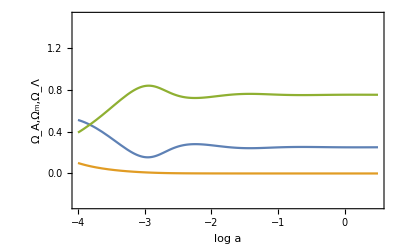

```mathematica
xiin=-.5;Plot[{omegaas[-4,xiin,om0x,t]/.t->tx,omes[-4,xiin,om0x,t]/.t->tx,1-(omes[-4,xiin,om0x,t]/.t->tx)-(omegaas[-4,xiin,om0x,t]/.t->tx)},{tx,-4,t0},Frame->True,FrameLabel->{"log a","Ω_A,Ω_m,Ω_Λ"},BaseStyle->{Large,FontFamily->"Times",FontSize->18},PlotRange->{-.3,1.5}]
```

## Diff eq. without CC

```mathematica
(* equations *)

Clear[α];xisecd=1/(9 (6+5 xi[n]) α)(xi[n] (6+5 xi[n])^2 (9 (16+α)+6 xi[n] (40+α)+xi[n]^2 (100+α))+6 (6+5 xi[n])^4 ome[n]-27 (6+11 xi[n]+5 xi[n]^2) α xi'[n]+135 α (xi'[n])^2);
omed=-(3+2*xi[n])*ome[n];
```

```mathematica
(* init cond now impose omega_lambda=0 *)
Clear[xi,α,w];

t0=.5;α=-4;

w=0;

Clear[dsol,xis,omes];
xipin=((6+5 xiin) (-4 om0x (6+5 xiin)^2+9 (16+α)+6 xiin (40+α)+xiin^2 (100+α)))/(18 α);
dsol[ti_,xi0_,om0_]:=NDSolve[{xi''[n]==xisecd,ome'[n]==omed,xi'[ti]==((6+5 xi0) (-4 om0 (6+5 xi0)^2+9 (16+α)+6 xi0 (40+α)+xi0^2 (100+α)))/(18 α),xi[ti]==xi0,ome[ti]==om0},{xi,ome},{n,ti,t0}];
xis[ti_,xi0_,om0_,n_]:=(xi/.dsol[ti,xi0,om0][[1]])[n]
xisp[ti_,xi0_,om0_,nx_]:=D[xis[ti,xi0,om0,n],n]/.n->nx;
omes[ti_,xi0_,om0_,n_]:=(ome/.dsol[ti,xi0,om0][[1]])[n]
omegaas[ti_,xi0_,om0_,n_]:=-α((xis[ti,xi0,om0,n]+3)^2*(5*xis[ti,xi0,om0,n]+6)-18*xisp[ti,xi0,om0,n])/(4*(5*xis[ti,xi0,om0,n]+6)^3)
```

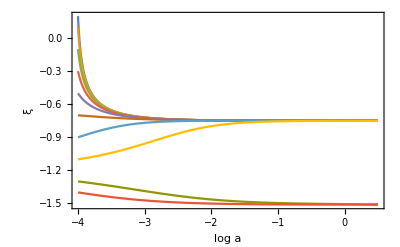

```mathematica
(* no cosm const *)
om0x=0.1;Plot[{xis[-4,.2,om0x,t]/.t->tx,xis[-4,.1,om0x,t]/.t->tx,xis[-4,-.1,om0x,t]/.t->tx,xis[-4,-.3,om0x,t]/.t->tx,xis[-4,-.5,om0x,t]/.t->tx,xis[-4,-.7,om0x,t]/.t->tx,xis[-4,-.9,om0x,t]/.t->tx,xis[-4,-1.1,om0x,t]/.t->tx,,xis[-4,-1.3,om0x,t]/.t->tx,xis[-4,-1.4,om0x,t]/.t->tx},{tx,-4,t0},Frame->True,FrameLabel->{"log a","ξ"},BaseStyle->{Large,FontFamily->"Times",FontSize->18}]
```

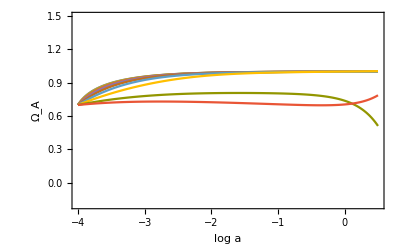

```mathematica
om0x=0.3;Plot[{omegaas[-4,.2,om0x,t]/.t->tx,omegaas[-4,.1,om0x,t]/.t->tx,omegaas[-4,-.1,om0x,t]/.t->tx,omegaas[-4,-.3,om0x,t]/.t->tx,omegaas[-4,-.5,om0x,t]/.t->tx,omegaas[-4,-.7,om0x,t]/.t->tx,omegaas[-4,-.9,om0x,t]/.t->tx,omegaas[-4,-1.1,om0x,t]/.t->tx,,omegaas[-4,-1.3,om0x,t]/.t->tx,omegaas[-4,-1.4,om0x,t]/.t->tx},{tx,-4,t0},Frame->True,PlotRange->{-.2,1.5},FrameLabel->{"log a","Ω_A"},BaseStyle->{Large,FontFamily->"Times",FontSize->18}]
```